```mathematica
SetDirectory["/home/rpb/worker-big/membrane-repository/pickle-repository/membrane-v612.md.part0003.skip10-framefilter-fixedaxis/"];
Needs["PlotLegends`"]
```

```mathematica
lenscale=20;
```

```mathematica
rot[th_]:={{Cos[th],-Sin[th]},{Sin[th],Cos[th]}}
```

#### Fixed axis

```mathematica
fx[x_,y_]:=-hpp*Exp[-(x-xcpp)^2/(2w1pp)]*Exp[-(y-ycpp)^2/(2w2pp)]
```

#### Fluid axis

```mathematica
fx[x_,y_]:=-hpp*Exp[-((x-xcpp)*Cos[theta]+(y-ycpp)*Sin[theta])^2/(2w1pp^2)]*Exp[-(-(x-xcpp)Sin[theta]+(y-ycpp)Cos[theta])^2/(2w2pp^2)]+zshift
```

```mathematica
curvfx[x_,y_]:=((1+D[fx[x,y],{x,1}]^2)D[fx[x,y],{y,2}]+(1+D[fx[x,y],{y,1}]^2)D[fx[x,y],{x,2}]-2*D[fx[x,y],{x,1}]*D[fx[x,y],{y,1}]*D[fx[x,y],{x,1},{y,1}])/(1+(D[fx[x,y],{x,1}])^2+(D[fx[x,y],{y,1}])^2)^(3/2)
```

#### Load parameters

```mathematica
filename="params.dat";
file=OpenRead[filename];
paramfile=ReadList[file,{Number,Number,Number,Number,Number,Number,Number}];
Close[file];
```

```mathematica
rawfile
```

{{14,14,17.8328},{14,15,18.1534},{14,16,16.6453},{14,17,14.7277},{14,18,13.2436},{14,19,14.6393},{14,20,14.4866},{14,21,11.4594},{15,14,22.1657},{15,15,16.9786},{15,16,16.8564},{15,17,15.6848},{15,18,17.0396},{15,19,15.9067},{15,20,11.3153},{15,21,10.5962},{16,14,18.8831},{16,15,16.9667},{16,16,16.1387},{16,17,15.1961},{16,18,14.7402},{16,19,13.9124},{16,20,10.2689},{16,21,11.1877},{17,14,19.4724},{17,15,15.4086},{17,16,13.411},{17,17,11.0784},{17,18,9.73923},{17,19,14.2654},{17,20,9.0543},{17,21,10.4365},{18,14,12.4954},{18,15,9.04457},{18,16,7.67276},{18,17,8.14443},{18,18,5.30898},{18,19,7.23229},{18,20,6.02828},{18,21,6.06084},{19,14,5.0508},{19,15,2.57807},{19,16,0.875371},{19,17,-0.116283},{19,18,-0.34854},{19,19,2.95408},{19,20,1.59025},{19,21,5.87407}}

#### Framewise calculation of maximum curvature

```mathematica
Dynamic[frameno]
curves={};
domains={};
regions={};
maps={};
cplotzs={};
curves2={};
params={};
means={};
dats={};
Clear[a,b,c,ap,bp,cp,w1p,w2p,hp,xcp,ycp,w1,w2,h,xc,yc,zshift,t1];
For[frameno=1,frameno≤400,frameno++,{Clear[a,b,c,ap,bp,cp,w1p,w2p,hp,xcp,ycp,w1,w2,h,xc,yc,zshift,t1];
filename="framefilter."<>ToString[NumberForm[frameno,{4,0},NumberPadding->{"0",""}]]<>"dat";
file=OpenRead[filename];
rawfile=ReadList[file,{Number,Number,Number}];
Close[file];
datar=rawfile;
{a,b,c1,c2,w1,w2,t1}=paramfile[[frameno]];
curvfx2[x_,y_]=curvfx[x,y]/.{hpp->b,xcpp->c1,ycpp->c2,w1pp->Sqrt[Abs[w1]/2],w2pp->Sqrt[Abs[w1]/2],zshift->a,theta->t1};
AppendTo[curves2,Max[Table[curvfx2[lenscale*datar[[i,1]],lenscale*datar[[i,2]]],{i,1,Length[datar]}]]];
regplot=ListPlot[Table[{lenscale*datar[[i,1]],lenscale*datar[[i,2]]},{i,1,Length[datar]}],AspectRatio->1,PlotStyle->{{PointSize[0.006],Gray}}];
AppendTo[regions,regplot];
}];
```

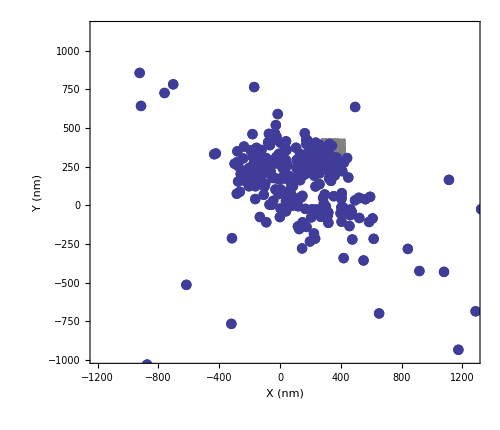

```mathematica
postraj=Table[{paramfile[[i,3]]+shifter[[1]],paramfile[[i,4]]+shifter[[2]]},{i,1,Length[paramfile]}];
lptraj=ListPlot[postraj,Frame->True,ClippingStyle->Opacity[1],PlotStyle->{{PointSize[0.015]}},FrameLabel->{"X (nm)","Y (nm)","Gaussian Center locations",""},BaseStyle->{14,FontFamily->"Helvetica",Bold}];
plotregions=Show[Table[regions[[i]],{i,1,Length[regions],100}]];
Show[lptraj,plotregions,lptraj,AspectRatio->Automatic,ImageSize->500,Axes->False]
```

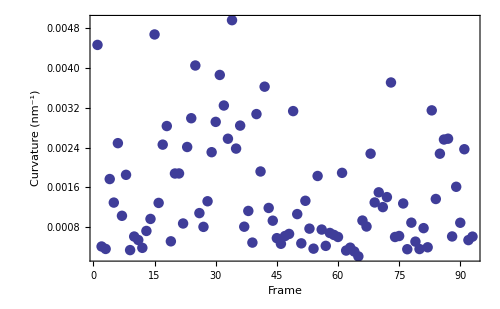

```mathematica
validinds=Position[Table[If[curves2[[i]]≤0.05&&curves2[[i]]≥0.001,1,0],{i,1,Length[curves2]}],1];
curvesv=Table[curves2[[validinds[[i,1]]]]/10.,{i,1,Length[validinds]}];
ListPlot[curvesv,PlotRange->All,ImageSize->500,Frame->True,PlotStyle->{{PointSize[0.015]}},FrameLabel->{"Frame","Curvature (nm^-1)","Filtered Curvature",""},Axes->False,BaseStyle->{14,FontFamily->"Helvetica",Bold}]
```

```mathematica
ListPlot[curvesv,PlotRange->All,ImageSize->500,Frame->True,PlotStyle->{{PointSize[0.015]}},FrameLabel->{"Frame","Curvature (nm^-1)","Filtered Curvature",""},Axes->False,BaseStyle->{14,FontFamily->"Helvetica",Bold}]
```

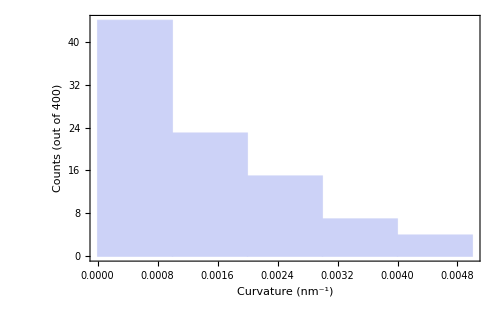

```mathematica
Histogram[curvesv,PlotRange->All,ImageSize->500,Frame->True,FrameLabel->{"Curvature (nm^-1)","Counts (out of 400)","Filtered maximum curvatures in the shadow",""},Axes->False,BaseStyle->{14,FontFamily->"Helvetica",Bold}]
```